```mathematica
σ0[r_]:=1-0.3 ⅇ^(-(r/3)^2)
u0[r_]:=√2 0.5 ⅇ^(-(r/3)^2)
```

```mathematica
(*Bag[0.01,0,0.5,24,300]*)
```

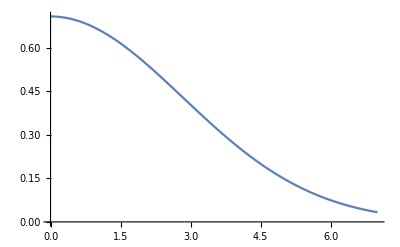

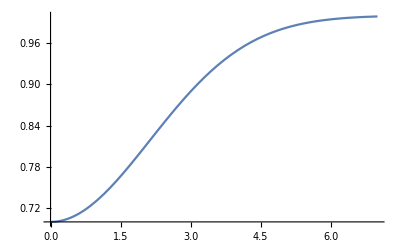

```mathematica
Plot[u0[r],{r,0,7}]
Plot[σ0[r],{r,0,7}]
```

```mathematica
Bag[κ_,ϵ0_,δϵ_,Rin_,in_,out_,n_]:=(
h=Rin/n;
R=Rin;
ϵ=ϵ0;
For[k=in,k≤out,k++,
ω[k]=ϵ;
U[σ_]:=1/8(σ^2-1)^2;
dU[σ_]:=1/2(σ^2-1)σ;
(*σ equations*)
eqσ[0]=6(σ[1]-σ[0])==h^2(dU[2/3 σ[0]+1/3 σ[1]]+κ^2(2/3 u[0]+1/3 u[1])^2(2/3 σ[0]+1/3 σ[1]));
Table[eqσ[i]=(1-h/2 2/(i h))σ[i-1]-2 σ[i]+(1 +h/2 2/(i h))σ[i+1]==h^2(dU[1/6 σ[i-1]+2/3 σ[i]+1/6 σ[i+1]]+κ^2(1/6 u[i-1]+2/3 u[i]+1/6 u[i+1])^2(1/6 σ[i-1]+2/3 σ[i]+1/6 σ[i+1])),{i,1,n}];
eqσ[n+1]=1/6(σ[n-1]+4σ[n]+σ[n+1])+R/(1+R)1/(2h)(-σ[n-1]+σ[n+1])==1;
(*u equations*)
equ[0]=6(u[1]-u[0])==h^2(κ^2(2/3 σ[0]+1/3 σ[1])^2-ϵ^2)(2/3 u[0]+1/3 u[1]);
Table[equ[i]=(1-h/2 2/(i h))u[i-1]-2 u[i]+(1 +h/2 2/(i h))u[i+1]==h^2((κ^2(1/6 σ[i-1]+2/3 σ[i]+1/6 σ[i+1])^2-ϵ^2)(1/6 u[i-1]+2/3 u[i]+1/6 u[i+1])),{i,1,n}];
equ[n+1]=(1/6(√(1-ϵ^2)+1/R)-1/(2h))u[n-1]+2/3(√(1-ϵ^2)+1/R)u[n]+(1/6(√(1-ϵ^2)+1/R)+1/(2 h))u[n+1]==0;
(*initial approximation for σ*)
Table[σineq[i]=1/6 σin[i-1]+2/3 σin[i]+1/6 σin[i+1]==σ0[i h],{i,0,n}];
σineq[-1]=σin[-1]==σin[1]; σineq[n+1]=σin[n-1]==σin[n+1];
σinappr=(*Table[σin[j],{j,-1,n+1}]/.*)NSolve[Table[σineq[i],{i,-1,n+1}],Table[σin[j],{j,-1,n+1}]];
(*initial approximation for u*)
Table[uineq[i]=1/6 uin[i-1]+2/3 uin[i]+1/6 uin[i+1]==u0[i h],{i,0,n}];
uineq[-1]=uin[-1]==uin[1];uineq[n+1]=uin[n-1]==uin[n+1];
uinappr=(*Table[σin[j],{j,-1,n+1}]/.*)NSolve[Table[uineq[i],{i,-1,n+1}],Table[uin[j],{j,-1,n+1}]];
(*Solver*)
equations=Join[Table[eqσ[i],{i,0,n+1}],Table[equ[i],{i,0,n+1}]];
variables=Join[Table[{σ[i],σin[i]},{i,0,n+1}],Table[{u[i],uin[i]},{i,0,n+1}]]/.σinappr/.uinappr;
sol=FindRoot[equations,variables[[1,1]]];
σprofile=Table[{i h,1/6(σ[i-1]+4 σ[i]+σ[i+1])},{i,0,n}]/.σ[-1]->σ[1]/.sol;
uprofile=Table[{i h,1/6(u[i-1]+4 u[i]+u[i+1])},{i,0,n}]/.u[-1]->u[1]/.sol;
σcoeff[k]=Table[{h i,σ[i]},{i,-1,n+1}]/.σ[-1]->σ[1]/.sol;
ucoeff[k]=Table[{h i,u[i]},{i,-1,n+1}]/.u[-1]->u[1]/.sol;
η[k]=4 π h Sum[(i h)^2 ϵ(1/6 u[i-1]+2/3 u[i]+1/6 u[i+1])^2/.sol,{i,0,n}];
H[k]=η[k]ϵ+4 π h Sum[(i h)^2(1/2(-(σ[i-1]-σ[i+1])/(2h))^2+U[1/6 σ[i-1]+2/3 σ[i]+1/6 σ[i+1]])/.sol,{i,0,n}];
σ0[x_]:=Piecewise[{{Sum[σ[i]BSplineBasis[{3,{(i-2)h,(i-1)h,i h,(i+1)h,(i+2)h}},0,x],{i,-1,n+1}]/.σ[-1]->σ[1]/.sol,x<R},{1,x≥R}}];
u0[x_]:=Sum[u[i]BSplineBasis[{3,{(i-2)h,(i-1)h,i h,(i+1)h,(i+2)h}},0,x],{i,-1,n+1}]/.u[-1]->u[1]/.sol;
time=1;
While[σprofile[[time,2]]<(1-10^-2),time++];
R=2(time-1)h;
box[k]=R;
h=R/n;
ϵ=ϵ0-k δϵ;
]
)
```

```mathematica
(*Bag[κ_,ϵ0_,δϵ_,Rin_,in_,out_,n_]*)
```

```mathematica
Bag[1,0.93,0.001,15,1,100,400]
```

```mathematica
{ω[100],N[box[100]]}
```

{0.831,13.2076}

```mathematica
(*Profiles drawn by  with dots*)
```

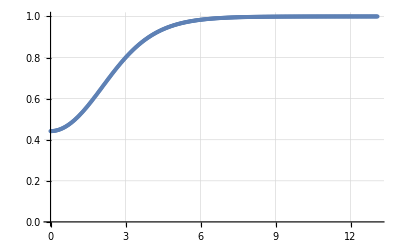

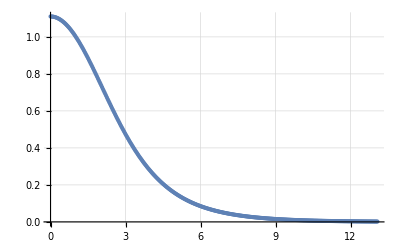

```mathematica
ListPlot[σprofile,PlotRange->Full,GridLines->Automatic]
ListPlot[uprofile,PlotRange->Full,GridLines->Automatic]
```

```mathematica
(*Cross-check*)
```

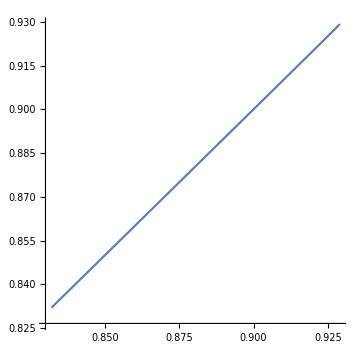

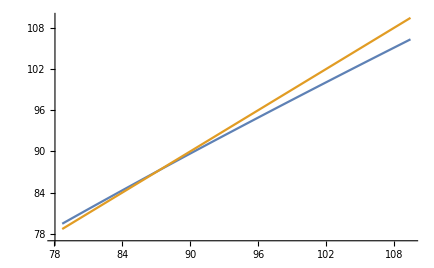

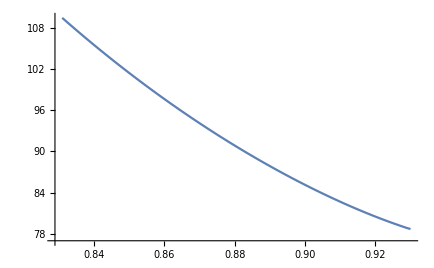

```mathematica
num=100;
ListLinePlot[Table[{ω[k],(H[k-1]-H[k+1])/(η[k-1]-η[k+1])},{k,2,num-1}],AspectRatio->1,ImageSize->Medium]
ListLinePlot[{Table[{η[k],H[k]},{k,1,num}],Table[{η[k],η[k]},{k,1,num}]}]
ListLinePlot[Table[{ω[k],η[k]},{k,1,num}]]
```

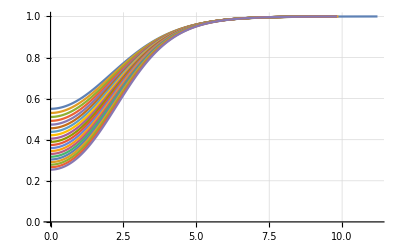

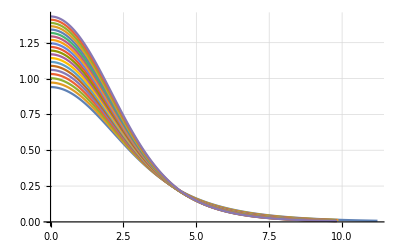

```mathematica
num=100;
interval=5;
Nx=300;
ListLinePlot[Table[Table[{σcoeff[k][[i+1,1]],1/6(σcoeff[k][[i,2]]+4σcoeff[k][[i+1,2]]+σcoeff[k][[i+2,2]])},{i,1,Nx}],{k,1,num,interval}],PlotRange->Full,GridLines->Automatic]
ListLinePlot[Table[Table[{ucoeff[k][[i+1,1]],1/6(ucoeff[k][[i,2]]+4ucoeff[k][[i+1,2]]+ucoeff[k][[i+2,2]])},{i,1,Nx}],{k,1,num,interval}],PlotRange->Full,GridLines->Automatic]
```